# rydberg-rydberg interactions

P. Huft

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\gothr\Documents\Graduate Research\Mathematica

## general setup

```mathematica
(*CONSTANTS*)
ℏ=1;
ee= 1.602*^-19;
c = 3*10^8;
μ0 =4π*10^-7;
ϵ0 = 1/√(c μ0);
qq = ee^2/(4 π ϵ0);

(*FUNCTIONS*)
OuterProd[A_,B_]:=Outer[Times,A,B]; (*outer product of vectors or matrices A,B*)
HamiltonianProduct[hsingle_,volume_ ]:=Module[
{totalham=hsingle},
(*the Hamiltonian describing the combined space of `volume` number of quantum systems with individual Hamiltonian hsingle*)
For[i=1,i<volume,i++,
totalham = KroneckerProduct[IdentityMatrix[Length[ham]],totalham] + KroneckerProduct[ham,IdentityMatrix[Length[totalham]]];
];
totalham
];
```

## single Rydberg state

### algebra

Single atom dipole matrix elements to be computed with PairInteraction module in python.

Single atom structure: include two ground states, intermediate excited state, Rydberg state. Assume that large Zeeman shifts isolate an effective 4 level lambda system.

Matrix elems. reshape H into atoms*states x atoms*states. 
H_(4 atomi - statei+1,4atomj-statej+1)=Δ_g1 δ_ij δ_(statei,1)δ_(statej,1)+Δ_g2 δ_ij δ_(statei,2)δ_(statej,2)+Δ_e δ_ij δ_(statei,3)δ_(statej,3)+ℏΩ_(1A)(δ_ij δ_(statei,2)δ_(statej,3)+δ_ij δ_(statei,3)δ_(statej,2))/2+ℏΩ_(1B)(δ_ij δ_(statei,1)δ_(statej,3)+δ_ij δ_(statei,3)δ_(statej,1))/2+ℏΩ_2(δ_ij δ_(statei,3)δ_(statej,4)+δ_ij δ_(statei,4)δ_(statej,3))/2+ (1-δ_ij)δ_(statei,4)δ_(statej,4)Vdd
Computationally more friendly to define a matrix Hij that describes the energy levels and coupling scheme of atom i, plus the interactions to atom j. Then just build Hfull by iterating over Hfull and plopping in Hij at each section atom x atom section.hmmm this is mixing a single atom basis with a two-atom basis... doesn’t really make sense as framed.

```mathematica
Hi =({{0, 0, Ω1B, 0}, {0, Δg1, Ω1A, 0}, {Ω1B*, Ω1A*, Δe1, Ω2}, {0, 0, Ω2*, Δr}});
```

test building the hamiltonian with kronecker products using only two-level systems

```mathematica
H1=({{0, Ω1/2}, {Ω1/2, Δ1}});
H2=({{0, Ω2/2}, {Ω2/2, Δ2}});
H12 =KroneckerProduct[IdentityMatrix[2],H1] + KroneckerProduct[H2,IdentityMatrix[2]];
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0
Ω1/2 | Δ1 | 0 | Ω2/2
Ω2/2 | 0 | Δ2 | Ω1/2
0 | Ω2/2 | Ω1/2 | Δ1+Δ2)

Now three atoms:

```mathematica
H3=({{0, Ω3/2}, {Ω3/2, Δ3}});
KroneckerProduct[IdentityMatrix[2],H12] + KroneckerProduct[H3,IdentityMatrix[4]];
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
Ω1/2 | Δ1 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
Ω2/2 | 0 | Δ2 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2 | 0 | 0 | 0 | Ω3/2
Ω3/2 | 0 | 0 | 0 | Δ3 | Ω1/2 | Ω2/2 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3 | 0 | Ω2/2
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3 | Ω1/2
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3)

What is the basis of this Hamiltonian?
{123g,1e,2e,12e,3e,13e,23e,123e}
The singly-excited state is given by (1/√3){0,1,1,0,1,0,0,0}

### rabi flopping - two level example

```mathematica
(*single atom Hamiltonian with effective basis {g,e}*)
Clear[Ω,Δ];
numStates=2; (*single atom states*)
numAtoms = 2;
atomBasis = IdentityMatrix[numStates];
Hsingle=({{0, Ω/2}, {Ω/2, Δ}});(*assume real Rabi freq.*)
Hint = ConstantArray[0,{numAtoms numStates,numAtoms numStates}];
Hint[[numAtoms numStates,numAtoms numStates]]=ΩB; (*interaction Hamiltonian*)
```

```mathematica
(*two-atom hamiltonian*)
Hmulti =KroneckerProduct[IdentityMatrix[numStates],Hsingle]+KroneckerProduct[Hsingle,IdentityMatrix[numStates]];
Hmulti//MatrixForm
```

(0 | Ω/2 | Ω/2 | 0
Ω/2 | Δ | 0 | Ω/2
Ω/2 | 0 | Δ | Ω/2
0 | Ω/2 | Ω/2 | 2 Δ)

```mathematica
(*add the r-r interaction*)
```

how to correctly add blockade terms with more than two atoms?

```mathematica
(*Build the initial array state and eqs to solve*)
Ω=2π;
Δ=0;
ΩB=0Ω;
hamiltonian = Hmulti+Hint;
ψ = Array[Subscript[P, #][t]&,numAtoms numStates];
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<numAtoms numStates+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,ψ0,sys};
tmax=3;
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
```

Time to run sim: 0 mins

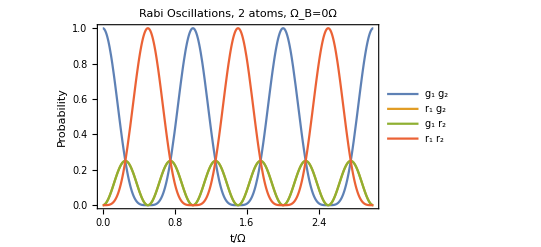

```mathematica
leg = {"g_1 g_2","r_1 g_2","g_1 r_2","r_1 r_2"};
plt=Plot[Evaluate[Abs[soln]^2],{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Rabi Oscillations, `` atoms, Ω_B=``Ω",numAtoms,ΩB/Ω],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
(*Export[ToString[StringForm["plot_rabi_flop_``atoms_``states_blockaded``.png",numAtoms,numStates,ΩB/Ω]],plt]*)
```

### rabi flopping - 2 or more atoms in uniform blockade

```mathematica
Clear[Ω,Δ];
numStates=2; (*single atom states*)
numAtoms = 4;
atomBasis = IdentityMatrix[numStates];
Hsingle=({{0, Ω/2}, {Ω/2, Δ}});(*assume real Rabi freq.*)

(*construct interaction Hamiltonian*)
Hint = ConstantArray[0,{numAtoms numStates,numAtoms numStates}];

Hint[[]]
```

```mathematica
(*Build the initial array state and eqs to solve*)
Ω=2π;
Δ=0;
ΩB=0Ω;
hamiltonian = Hmulti+Hint;
ψ = Array[Subscript[P, #][t]&,numAtoms numStates];
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<numAtoms numStates+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,ψ0,sys};
tmax=3;
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
```

```mathematica
leg = {"g_1 g_2","r_1 g_2","g_1 r_2","r_1 r_2"};
plt=Plot[Evaluate[Abs[soln]^2],{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Rabi Oscillations, `` atoms, Ω_B=``Ω",numAtoms,ΩB/Ω],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

## misc testing

write recursive function to build multi-atom Hamiltonian by successively combining the single atom subspaces.

```mathematica
(*single atom Hamiltonian with effective basis {g,e}*)
Clear[Ω,Δ];
numStates=2; (*single atom states*)
numAtoms = 2;
H1=({{0, Ω/2}, {Ω/2, Δ}});(*assume real Rabi freq.*)
H2int = ConstantArray[0,{numAtoms numStates,numAtoms numStates}];
H2int[[numAtoms numStates,numAtoms numStates]]=ΩB; (*interaction Hamiltonian*)
```

test building the hamiltonian with kronecker products using only two-level systems

```mathematica
H1=({{0, Ω1/2}, {Ω1/2, Δ1}});
H2=({{0, Ω2/2}, {Ω2/2, Δ2}});
H12 =KroneckerProduct[IdentityMatrix[Length[H2]],H1] + KroneckerProduct[H2,IdentityMatrix[Length[H1]]];
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0
Ω1/2 | Δ1 | 0 | Ω2/2
Ω2/2 | 0 | Δ2 | Ω1/2
0 | Ω2/2 | Ω1/2 | Δ1+Δ2)

Now add the blockade:

```mathematica
H12int = ConstantArray[0,Dimensions[H12]];
(*H12int[[-1,-1]]=ΩB12;*)
(*H12=H12+H12int;*)
H12//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0
Ω1/2 | Δ1 | 0 | Ω2/2
Ω2/2 | 0 | Δ2 | Ω1/2
0 | Ω2/2 | Ω1/2 | Δ1+Δ2)

Now three atoms:

```mathematica
H3=({{0, Ω3/2}, {Ω3/2, Δ3}});
H123=KroneckerProduct[IdentityMatrix[Length[H1]],H12] + KroneckerProduct[H3,IdentityMatrix[Length[H12]]];
H123//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
Ω1/2 | Δ1 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
Ω2/2 | 0 | Δ2 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2 | 0 | 0 | 0 | Ω3/2
Ω3/2 | 0 | 0 | 0 | Δ3 | Ω1/2 | Ω2/2 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3 | 0 | Ω2/2
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3 | Ω1/2
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3)

```mathematica
H4=({{0, Ω4/2}, {Ω4/2, Δ4}});
H1234=KroneckerProduct[IdentityMatrix[Length[H1]],H123] + KroneckerProduct[H4,IdentityMatrix[Length[H123]]];
```

```mathematica
H1234//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω1/2 | Δ1 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0
Ω2/2 | 0 | Δ2 | Ω1/2 | 0 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2 | 0 | 0 | 0 | Ω3/2 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0
Ω3/2 | 0 | 0 | 0 | Δ3 | Ω1/2 | Ω2/2 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3 | 0 | Ω2/2 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3 | Ω1/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω4/2
Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ4 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω1/2 | Δ1+Δ4 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | Ω2/2 | 0 | Δ2+Δ4 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | 0 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ4 | 0 | 0 | 0 | Ω3/2
0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | 0 | 0 | Δ3+Δ4 | Ω1/2 | Ω2/2 | 0
0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3+Δ4 | 0 | Ω2/2
0 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3+Δ4 | Ω1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω4/2 | 0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3+Δ4)

Try to add in the blockade interaction in a straightforward way:

```mathematica
Clear[ΩB];
H1=({{0, Ω1/2}, {Ω1/2, Δ1}});
H2=({{0, Ω2/2}, {Ω2/2, Δ2}});
H12int = ConstantArray[0,{4,4}];
H12int[[4,4]]=ΩB12; 
H12 =KroneckerProduct[IdentityMatrix[Length[H2]],H1] + KroneckerProduct[H2,IdentityMatrix[Length[H1]]]+H12int;
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0
Ω1/2 | Δ1 | 0 | Ω2/2
Ω2/2 | 0 | Δ2 | Ω1/2
0 | Ω2/2 | Ω1/2 | Δ1+Δ2+ΩB12)

```mathematica
H3=({{0, Ω3/2}, {Ω3/2, Δ3}});
H13 =KroneckerProduct[IdentityMatrix[Length[H3]],H12] + KroneckerProduct[H3,IdentityMatrix[Length[H12]]];
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
Ω1/2 | Δ1 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
Ω2/2 | 0 | Δ2 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2+ΩB12 | 0 | 0 | 0 | Ω3/2
Ω3/2 | 0 | 0 | 0 | Δ3 | Ω1/2 | Ω2/2 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3 | 0 | Ω2/2
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3 | Ω1/2
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3+ΩB12)

```mathematica
H13int = H12int = ConstantArray[0,{4,4}];
H13int[[4,4]]=ΩB13; 
H23int = H12int = ConstantArray[0,{4,4}];
H23int[[4,4]]=ΩB23; 
(*H12 =KroneckerProduct[IdentityMatrix[Length[H2]],H1] + KroneckerProduct[H2,IdentityMatrix[Length[H1]]];
%//MatrixForm*)
```

```mathematica
KroneckerProduct[IdentityMatrix[Length[H3]],H13int];
%//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ΩB13 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩB13)

```mathematica
H3
```

{{0,Ω3/2},{Ω3/2,Δ3}}

```mathematica
H13
```

{{0,Ω1/2,Ω2/2,0,Ω3/2,0,0,0},{Ω1/2,Δ1,0,Ω2/2,0,Ω3/2,0,0},{Ω2/2,0,Δ2,Ω1/2,0,0,Ω3/2,0},{0,Ω2/2,Ω1/2,Δ1+Δ2+ΩB12,0,0,0,Ω3/2},{Ω3/2,0,0,0,Δ3,Ω1/2,Ω2/2,0},{0,Ω3/2,0,0,Ω1/2,Δ1+Δ3,0,Ω2/2},{0,0,Ω3/2,0,Ω2/2,0,Δ2+Δ3,Ω1/2},{0,0,0,Ω3/2,0,Ω2/2,Ω1/2,Δ1+Δ2+Δ3+ΩB12}}

```mathematica
KroneckerDelta[H12int,IdentityMatrix[4]]
```

```mathematica
H13int
```

```mathematica
ΩB
```

0

If we know what the basis is than we will know how to properly build the interaction Hamiltonian. 
{1000,0100,1100,0010,1010}... etc. So writing the states this way, denoting the jth atom in the subspace in its excited (ground) state with a 1 (0) in the jth position of the 4-atom ket, shows that the atoms involved in the blockade are gotten by looking at the non-zero places in the binary representation of the diagonal index. This pattern will change for a more complicated atom but this is a good start.

Now construct such a hamiltonian for an arbitrary number of quantum systems using a function

```mathematica
HamiltonianProduct[hsingle_,volume_ ]:=Module[
{totalham=hsingle},
(*the Hamiltonian describing the combined space of `volume` number of quantum systems with individual Hamiltonian hsingle*)
For[i=1,i<volume,i++,
totalham = KroneckerProduct[IdentityMatrix[Length[ham]],totalham] + KroneckerProduct[ham,IdentityMatrix[Length[totalham]]];
];
totalham
];
```

```mathematica
HamiltonianProduct[Hsingle,4]//MatrixForm
```

(0 | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | 0 | Δ | Ω/2 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0
0 | Ω/2 | Ω/2 | 2 Δ | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0
Ω/2 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0
0 | Ω/2 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0
0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 2 Δ | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0
0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 3 Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2
Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0
0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0
0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 2 Δ | Ω/2 | 0 | 0 | Ω/2 | 0
0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | Ω/2 | 3 Δ | 0 | 0 | 0 | Ω/2
0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 2 Δ | Ω/2 | Ω/2 | 0
0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | Ω/2 | 3 Δ | 0 | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 3 Δ | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 4 Δ)

```mathematica
ham = Hsingle;
volume=4; (*number of quantum system*)
totalham = Hsingle;
For[i=1,i<volume,i++,
totalham = KroneckerProduct[IdentityMatrix[Length[ham]],totalham] + KroneckerProduct[ham,IdentityMatrix[Length[totalham]]];
Print[totalham//MatrixForm]
]
```

(0 | Ω/2 | Ω/2 | 0
Ω/2 | Δ | 0 | Ω/2
Ω/2 | 0 | Δ | Ω/2
0 | Ω/2 | Ω/2 | 2 Δ)

(0 | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0
Ω/2 | Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0
Ω/2 | 0 | Δ | Ω/2 | 0 | 0 | Ω/2 | 0
0 | Ω/2 | Ω/2 | 2 Δ | 0 | 0 | 0 | Ω/2
Ω/2 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0
0 | Ω/2 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2
0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 2 Δ | Ω/2
0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 3 Δ)

(0 | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | 0 | Δ | Ω/2 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0
0 | Ω/2 | Ω/2 | 2 Δ | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0
Ω/2 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0
0 | Ω/2 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0
0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 2 Δ | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0
0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 3 Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2
Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ | Ω/2 | Ω/2 | 0 | Ω/2 | 0 | 0 | 0
0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 2 Δ | 0 | Ω/2 | 0 | Ω/2 | 0 | 0
0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 2 Δ | Ω/2 | 0 | 0 | Ω/2 | 0
0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 0 | 0 | Ω/2 | Ω/2 | 3 Δ | 0 | 0 | 0 | Ω/2
0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | 2 Δ | Ω/2 | Ω/2 | 0
0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | 0 | Ω/2 | 3 Δ | 0 | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | Ω/2 | 0 | 3 Δ | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 0 | 0 | 0 | Ω/2 | 0 | Ω/2 | Ω/2 | 4 Δ)

Generate the multi-atom blockade interaction matrix

```mathematica
OmegaB[i_,j_]:=KroneckerDelta[i,j]StringForm["ΩB````",i,j]; (*eventually this will be a realistic function*)
```

```mathematica
Bidcs=Table[]
```

ΩB13